## Phase Diagram: Basic 2D PFC

Firstly let’s define a set of k vectors for the amplitude expansion.

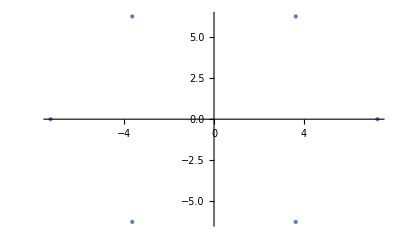

```mathematica
k[i_]:=q{Cos[2π i/6],Sin[2π i/6]};ListPlot[Table[k[i]/.q-> (4π)/(√3),{i,0,5}],PlotStyle->PointSize[Large]]
```

Then we sum up the various modes

```mathematica
Subscript[n, tri]=Subscript[n, 0]+Sum[ A ⅇ^(ⅈ k[i].{x,y}),{i,0,5}]//FullSimplify
```

2 A (Cos[q x]+2 Cos[(q x)/2] Cos[1/2 √3 q y])+n_0

```mathematica
k[1].{x,y}
```

(q x)/2+1/2 √3 q y

Now let’s start putting together the free energy

```mathematica
Subscript[f, ideal]=(Subscript[B, ℓ]/2 n^2-t/6 n^3+v/12 n^4)/.n-> Subscript[n, tri]
```

1/2 B_ℓ (2 A (Cos[q x]+2 Cos[(q x)/2] Cos[1/2 √3 q y])+n_0)^2-1/6 t (2 A (Cos[q x]+2 Cos[(q x)/2] Cos[1/2 √3 q y])+n_0)^3+1/12 v (2 A (Cos[q x]+2 Cos[(q x)/2] Cos[1/2 √3 q y])+n_0)^4

```mathematica
Subscript[f, excess]=1/2 Subscript[n, tri](Bx(2∇_{x,y}^2 Subscript[n, tri]+∇_{x,y}^2 (∇_{x,y}^2 Subscript[n, tri])))
```

1/2 Bx (15/4 A q^4 Cos[(q x)/2] Cos[1/2 √3 q y]+2 A (q^4 Cos[q x]+1/8 q^4 Cos[(q x)/2] Cos[1/2 √3 q y])+2 (-3 A q^2 Cos[(q x)/2] Cos[1/2 √3 q y]+2 A (-q^2 Cos[q x]-1/2 q^2 Cos[(q x)/2] Cos[1/2 √3 q y]))) (2 A (Cos[q x]+2 Cos[(q x)/2] Cos[1/2 √3 q y])+n_0)

Next let’s integrate over the unit cells to kill off all the Sines and Cosines. I’m going to do this one part at a time because I like to use pre-calculated integrals.

```mathematica
n2=q^2/(4 √3 π^2)∫_0^(√3(2π)/q) ∫_0^((2π)/q) Expand[(n^2/.n-> Subscript[n, tri])]ⅆxⅆy
n3=q^2/(4 √3 π^2)∫_0^(√3(2π)/q) ∫_0^((2π)/q) Expand[(n^3/.n-> Subscript[n, tri])]ⅆxⅆy
n4=q^2/(4 √3 π^2)∫_0^(√3(2π)/q) ∫_0^((2π)/q) Expand[(n^4/.n-> Subscript[n, tri])]ⅆxⅆy
```

6 A^2+n_0^2

12 A^3+18 A^2 n_0+n_0^3

90 A^4+48 A^3 n_0+36 A^2 n_0^2+n_0^4

```mathematica
Subscript[F, ideal]= (Subscript[B, ℓ]/2 n2-t/3 n3+v/4 n4)
```

1/2 B_ℓ (6 A^2+n_0^2)-1/3 t (12 A^3+18 A^2 n_0+n_0^3)+1/4 v (90 A^4+48 A^3 n_0+36 A^2 n_0^2+n_0^4)

```mathematica
Subscript[F, excess]=q^2/(4 √3 π^2)∫_0^(√3(2π)/q) ∫_0^((2π)/q) Expand[Subscript[f, excess]]ⅆxⅆy
```

3 A^2 Bx q^2 (-2+q^2)

Put these together and  let’s solve for the equilibrium q value

```mathematica
Subscript[F, tot]=Subscript[F, ideal]+Subscript[F, excess]
```

3 A^2 Bx q^2 (-2+q^2)+1/2 B_ℓ (6 A^2+n_0^2)-1/3 t (12 A^3+18 A^2 n_0+n_0^3)+1/4 v (90 A^4+48 A^3 n_0+36 A^2 n_0^2+n_0^4)

```mathematica
Subscript[q, eq]=Solve[D[Subscript[F, tot],q]==0,q]
```

{{q→-1},{q→0},{q→1}}

We’re going to take the  third  solution

```mathematica
Subscript[q, eq][[3]]
```

{q→1}

```mathematica
Subscript[F, tot]=Subscript[F, tot]/.Subscript[q, eq][[3]]
```

-3 A^2 Bx+1/2 B_ℓ (6 A^2+n_0^2)-1/3 t (12 A^3+18 A^2 n_0+n_0^3)+1/4 v (90 A^4+48 A^3 n_0+36 A^2 n_0^2+n_0^4)

And now let’s solve  for  the amplitude

```mathematica
Subscript[A, eq]=Solve[D[Subscript[F, tot],A]==0,A]
```

{{A→0},{A→(t-3 v n_0-√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))/(15 v)},{A→(t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))/(15 v)}}

We are going to take the first solution for the liquid and the third solution for the solid.

```mathematica
Subscript[F, ℓ]=Subscript[F, tot]/.Subscript[A, eq][[1]]
```

1/2 B_ℓ n_0^2-(t n_0^3)/3+(v n_0^4)/4

```mathematica
Subscript[F, s]=Subscript[F, tot]/.Subscript[A, eq][[3]]
```

-(Bx (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^2)/(75 v^2)+1/2 B_ℓ (n_0^2+(2 (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^2)/(75 v^2))-1/3 t (n_0^3+(2 n_0 (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^2)/(25 v^2)+(4 (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^3)/(1125 v^3))+1/4 v (n_0^4+(4 n_0^2 (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^2)/(25 v^2)+(16 n_0 (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^3)/(1125 v^3)+(2 (t-3 v n_0+√(t^2+15 Bx v-15 v B_ℓ+24 t v n_0-36 v^2 n_0^2))^4)/(1125 v^4))

Finally let’s put in some parameters and make a phase diagram

```mathematica
params={
t-> 1.0,
v-> 1.0,
Subscript[B, ℓ]-> 1.0
}
Subscript[F, ℓ]=Subscript[F, ℓ]/.params
Subscript[F, s]=Subscript[F, s]/.params
```

{t→1.,v→1.,B_ℓ→1.}

0.5 n_0^2-0.333333 n_0^3+0.25 n_0^4

-0.0133333 Bx (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^2+0.5 (n_0^2+0.0266667 (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^2)-0.333333 (n_0^3+0.08 n_0 (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^2+0.00355556 (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^3)+0.25 (n_0^4+0.16 n_0^2 (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^2+0.0142222 n_0 (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^3+0.00177778 (1.-3. n_0+√(-14.+15. Bx+24. n_0-36. n_0^2))^4)

For good measure let’s make a test plot at a ΔB value of 0.05

```mathematica
Plot[{Subscript[F, ℓ]/.Bx-> 0.95,Subscript[F, s]/.Bx-> 0.95},{Subscript[n, 0],-0.25,0.25},PlotStyle->{Blue,Red},PlotLabels->Automatic]
```

-Graphics-

Then the final thing we need to do is start finding common tangents. Because attempting to solve this directly can be a bit of a pain I tend to do this numerically by building the minimal energetic curve with some discretization and use a convex hull finder.

```mathematica
testF = Table[{nval, Min[Subscript[F, ℓ]/.{Subscript[n, 0]-> nval,Bx-> 1},If[Im[Subscript[F, s]/.{Subscript[n, 0]-> nval,Bx-> 1}]==0,Subscript[F, s]/.{Subscript[n, 0]-> nval,Bx-> 1},Subscript[F, ℓ]/.{Subscript[n, 0]-> nval,Bx-> 1}]]},{nval,-0.25,0.25,0.01}]
```

{{-0.25,0.0374349},{-0.24,0.0342374},{-0.23,0.0312053},{-0.22,0.028335},{-0.21,0.0256232},{-0.2,0.0230667},{-0.19,0.0206621},{-0.18,0.0184064},{-0.17,0.0162965},{-0.16,0.0143292},{-0.15,0.0125016},{-0.14,0.0108107},{-0.13,0.00925374},{-0.12,0.00782784},{-0.11,0.00653027},{-0.1,0.00535833},{-0.09,0.0043094},{-0.08,0.00338091},{-0.07,0.00257034},{-0.06,0.00187524},{-0.05,0.00129323},{-0.04,0.000821973},{-0.03,0.000220429},{-0.02,-0.000680495},{-0.01,-0.00155357},{0.,-0.00237037},{0.01,-0.00311317},{0.02,-0.00376942},{0.03,-0.00432966},{0.04,-0.00478654},{0.05,-0.00513423},{0.06,-0.00536806},{0.07,-0.00548433},{0.08,-0.00548011},{0.09,-0.00535311},{0.1,-0.00510162},{0.11,-0.0047244},{0.12,-0.00422064},{0.13,-0.00358994},{0.14,-0.00283218},{0.15,-0.0019476},{0.16,-0.000936681},{0.17,0.000199839},{0.18,0.001461},{0.19,0.00284563},{0.2,0.00435238},{0.21,0.00597974},{0.22,0.00772602},{0.23,0.00958943},{0.24,0.011568},{0.25,0.0136598}}

```mathematica
mesh = MeshPrimitives[ConvexHullMesh[testF],2][[1,1,;;,1]]
```

{-0.25,-0.24,-0.23,-0.22,-0.21,-0.2,-0.19,-0.18,-0.17,-0.16,-0.15,-0.14,-0.13,-0.12,-0.11,-0.1,-0.09,-0.08,-0.07,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25}

```mathematica
PDvalues={};
For[i = 1,i< Length[mesh],i++,
If[mesh[[i+1]] - mesh[[i]]>  0.01,
AppendTo[PDvalues,mesh[[i]]];
AppendTo[PDvalues,mesh[[i+1]]];
]
]
PDvalues
```

{-0.07,0.01}

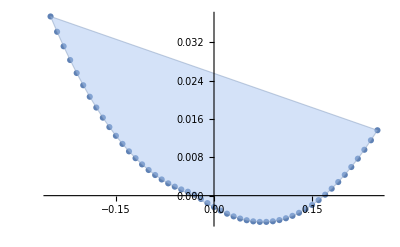

```mathematica
Show[ListPlot[testF],HighlightMesh[ConvexHullMesh[testF],Style[2,Opacity[0.5]]]]
```

This process is then repeated for a number of temperatures to build up a phase diagram.

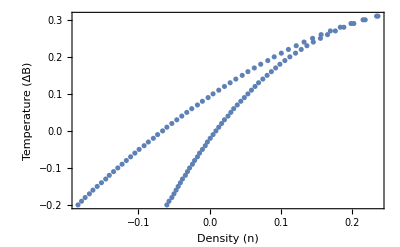

```mathematica
PDvalues={};
For[Bxval=0.4,Bxval≤ 1.2,Bxval+=0.01,
testF = Table[{nval, Min[Subscript[F, ℓ]/.{Subscript[n, 0]-> nval,Bx-> Bxval},If[Im[Subscript[F, s]/.{Subscript[n, 0]-> nval,Bx-> Bxval}]==0,Subscript[F, s]/.{Subscript[n, 0]-> nval,Bx-> Bxval},Subscript[F, ℓ]/.{Subscript[n, 0]-> nval,Bx-> Bxval}]]},{nval,-0.25,0.25,0.001}];
mesh = MeshPrimitives[ConvexHullMesh[testF],2][[1,1,;;,1]];
For[i = 1,i< Length[mesh],i++,
If[mesh[[i+1]] - mesh[[i]]>  0.001,
AppendTo[PDvalues,{mesh[[i]],1-Bxval}];
AppendTo[PDvalues,{mesh[[i+1]],1-Bxval}];
]
]
]
ListPlot[PDvalues,Frame->True,FrameLabel->{Style["Density (n)",Larger],Style["Temperature (ΔB)",Larger]}]
```